## Lower Saxony

```mathematica
Length@{1,4,10,18,19,21,33,49,75,129}
```

10

```mathematica
tab=Table[i,{i,11,20}]
```

{11,12,13,14,15,16,17,18,19,20}

```mathematica
nw2s=Transpose[{tab,{1,4,10,18,19,21,33,49,75,129}}]
```

{{11,1},{12,4},{13,10},{14,18},{15,19},{16,21},{17,33},{18,49},{19,75},{20,129}}

```mathematica
fitits=Normal@NonlinearModelFit[nw2s,b Exp[a t],{a,b},t]
```

0.0206203 ⅇ^(0.43544 t)

## Germany

```mathematica
Integrate[1/(N-n),n]
```

-Log[n-N]

```mathematica
FullSimplify[-Log[n-N]-Log[(n-N)^(-1)]]
```

-Log[1/(n-N)]-Log[n-N]

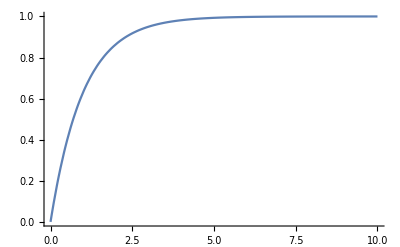

```mathematica
Plot[1-Exp[-t ],{t,0,10},PlotRange->All]
```

```mathematica
nw={{25,1},{26,2},{27,4},{28,25},{29,30},{30,30},{31,66},{32,86},{33,101},{34,111},{35,175},{36,281},{37,329}};
```

```mathematica
nw2=nw/.{xx_,yy_}->{xx-24,yy};
```

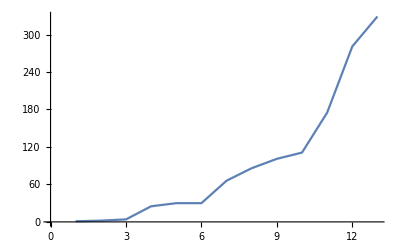

```mathematica
ListLinePlot[nw2]
```

```mathematica
dn/dt = A n
```

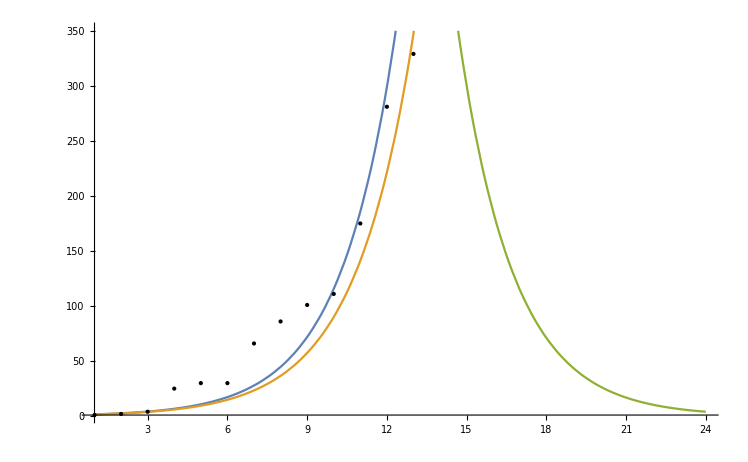

```mathematica
Plot[{Exp[0.475x],Exp[0.45x],300Exp[-0.48(x-15)]},{x,1,24},Epilog->{Point[nw2]},PlotRange->{{1,24},{1,350}}]
```

```mathematica
300Exp[-0.48(20-15)]
```

27.2154

```mathematica
Exp[0.475 *13]
```

480.583

```mathematica
nw={{25,1},{26,1},{27,1},{28,4},{29,10},{30,18},{31,19},{32,21},{33,33}};
```

```mathematica
nw2=nw/.{xx_,yy_}->{xx-24,yy};
```

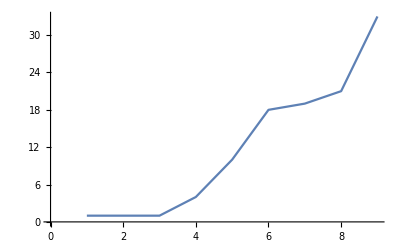

```mathematica
ListLinePlot[nw2]
```

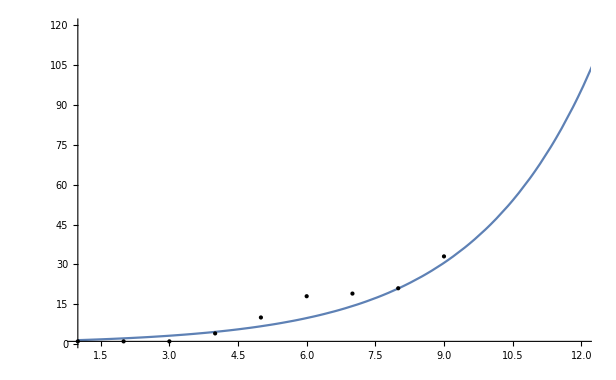

```mathematica
Plot[{Exp[0.38x]},{x,1,24},Epilog->{Point[nw2]},PlotRange->{{1,12},{1,120}}]
```

```mathematica
nwa={{24,16},{25,18},{26,21},{27,26},{28,53},{29,66},{30,117},{31,151},{32,188},{33,240},{34,349},{35,534},{36,684},{37,847},
{38,1112},{39,1296},{40,1565},{41,2369},{42,3062},{43,3795},{44,4838}};
```

```mathematica
nw2a=nwa/.{xx_,yy_}->{xx-23,yy}
```

{{1,16},{2,18},{3,21},{4,26},{5,53},{6,66},{7,117},{8,151},{9,188},{10,240},{11,349},{12,534},{13,684},{14,847},{15,1112},{16,1296},{17,1565},{18,2369},{19,3062},{20,3795},{21,4838}}

```mathematica
fitger=Normal@NonlinearModelFit[nw2a,b Exp[a t],{a,b},t]
```

21.4872 ⅇ^(0.258197 t)

```mathematica
mod2=Normal@NonlinearModelFit[nw2,c Tanh[a(x-10.1)]+d,{a,b,c,d},x]
```

1735.69+1671.94 Tanh[312.085 (-10.1+x)]

```mathematica
mod2=Normal@NonlinearModelFit[nw2,a Exp[b(x-10)]/(1-c(1-Exp[b(x-9)])),{a,b,c,d},x]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

(1184.81 ⅇ^(-0.0138765 (-10+x)))/(1-3.79847 (1-ⅇ^(-0.0138765 (-9+x))))

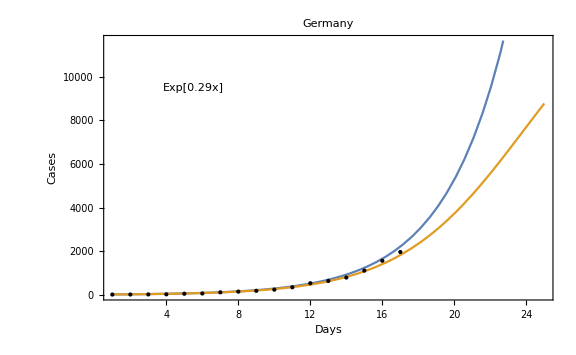

```mathematica
nmax=15000;Plot[{16Exp[0.29x],nmax/(1+(-15+nmax)/15Exp[-x 0.29])},{x,1,25},Epilog->{Point[nw2a]},Frame->True,FrameStyle->Directive[Black,Bold,16],FrameLabel->{"Days","Cases"},PlotLegends->Placed["Exp[0.29x]",{0.2,0.8}],ImageSize->Large,PlotLabel->"Germany"]
```

```mathematica
Exp[0.29*4]
```

3.18993

```mathematica
NSolve[1200/(2^n)==1,n]
NSolve[1200/(3^n)==1,n]
NSolve[1200/(4^n)==1,n]
```

{{n→ConditionalExpression[4.+1. (6.22882+(0.+9.06472 ⅈ) C[1]),C[1]∈ℤ]}}

{{n→ConditionalExpression[1.+1. (5.45367+(0.+5.7192 ⅈ) C[1]),C[1]∈ℤ]}}

{{n→ConditionalExpression[2.+1. (3.11441+(0.+4.53236 ⅈ) C[1]),C[1]∈ℤ]}}

```mathematica
nmaxchina=(3500*8/6.)*1.98
```

9240.

```mathematica
0.29*500 Exp[0.29 *7]
```

1104.04

```mathematica
0.29*500Exp[0.29 *6]
```

826.115

```mathematica
model=NonlinearModelFit[nw2,a^2/(b^2+(x-c)^2),{a,b,c},x]
```

FittedModel[4305.55/(6.6499+(-«19»+x)^2)]

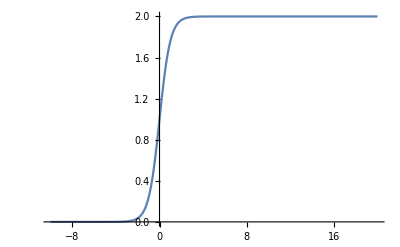

```mathematica
Plot[Tanh[x]+1,{x,-10,20}]
```

```mathematica
modeln=Normal@model
```

4305.55/(6.6499+(-13.2568+x)^2)

```mathematica
modelnerr=model["MeanPredictionBands"];
```

```mathematica
model2=NonlinearModelFit[nw2,c Exp[a (x-10)]/(1-b(1-Exp[a (x-10)])),{a,b,{x0,1},c},x]
```

FittedModel[(240. ⅇ^(1.72537×10^14«1»«1»))/(1-0.473062 (1-ⅇ^(«23» («1»))))]

```mathematica
model2n=Normal[model2]
```

(240. ⅇ^(1.72537×10^14 (-10+x)))/(1-0.473062 (1-ⅇ^(1.72537×10^14 (-10+x))))

General::munfl: Exp[-1.55273×10^15] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.55283×10^15] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

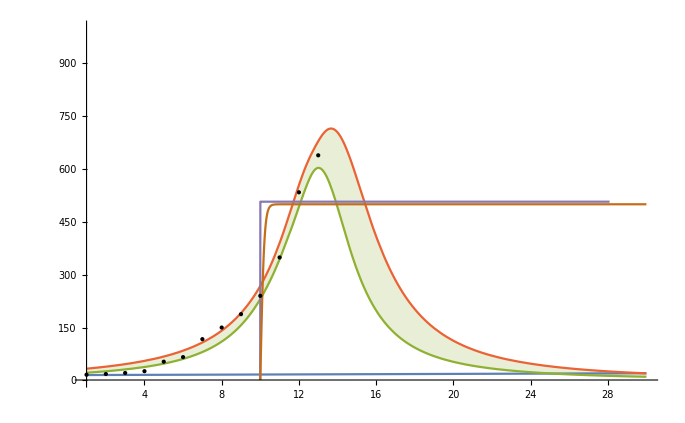

```mathematica
Plot[{15Exp[0.01x],model,modelnerr[[1]],modelnerr[[2]],model2n,500Tanh[5(x-10)]},{x,1,30},Epilog->{Point[nw2]},PlotRange->{{1,30},{1,1000}},Filling->{3->{4}}]
```

```mathematica
500*80/60.
```

666.667

```mathematica
D[Exp[0.29 x],x]
```

0.29 ⅇ^(0.29 x)

```mathematica
0.29 ⅇ^(0.29 20)
```

95.7869

```mathematica
0.6*0.03
```

0.018

## Spain

```mathematica
nws={{4,24},{8,25},{14,26},{26,27},{45,28},{59,29},{84,30},{125,31},{169,32},{228,33},{282,34},{365,35},{430,36},{674,37},{1231,38},{1695,39},{2277,40},{3146,41},{5232,42},{6391,43},{7798,44}};
```

```mathematica
nws=Transpose[{Transpose[nws][[2]],Transpose[nws][[1]]}]
```

{{24,4},{25,8},{26,14},{27,26},{28,45},{29,59},{30,84},{31,125},{32,169},{33,228},{34,282},{35,365},{36,430},{37,674},{38,1231},{39,1695},{40,2277},{41,3146},{42,5232},{43,6391},{44,7798}}

```mathematica
nw2sp=nws/.{xx_,yy_}->{xx-23,yy}
```

{{1,4},{2,8},{3,14},{4,26},{5,45},{6,59},{7,84},{8,125},{9,169},{10,228},{11,282},{12,365},{13,430},{14,674},{15,1231},{16,1695},{17,2277},{18,3146},{19,5232},{20,6391},{21,7798}}

```mathematica
fitsp=NonlinearModelFit[nw2sp,b Exp[a t],{b,a},t,MaxIterations->Infinity]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FittedModel[12.9005 ⅇ^(0.307686 t)]

```mathematica
fitspn=Normal@fitsp
```

12.9005 ⅇ^(0.307686 t)

```mathematica
fitspi=fitsp["MeanPredictionBands",ConfidenceLevel->0.99]
```

{12.9005 ⅇ^(0.307686 t)-2.86093 √(ⅇ^(0.615371 t) (10.502-1.05267 t+0.0265504 t^2)),12.9005 ⅇ^(0.307686 t)+2.86093 √(ⅇ^(0.615371 t) (10.502-1.05267 t+0.0265504 t^2))}

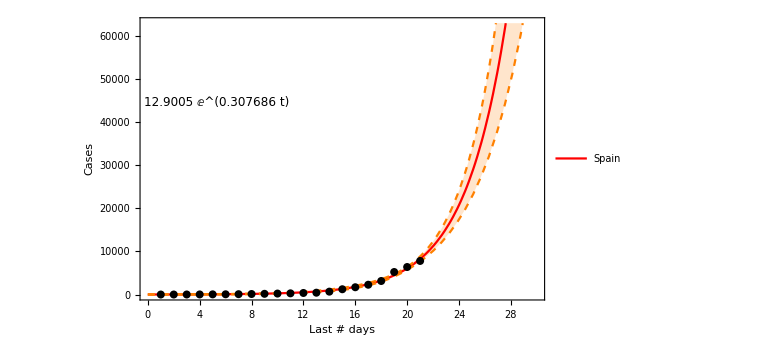

```mathematica
Plot[{fitspn,fitspi[[1]],fitspi[[2]]},{t,0,30},Epilog->{{Black,PointSize[0.01],Point[nw2sp]},{Text[Style[fitspn,Black,12],Scaled[{0.19,0.7}]]}},PlotStyle->{Directive[Red],Directive[Orange,Dashed],Directive[Orange,Dashed],Directive[Black,Dashed],Blue},Frame->True,FrameStyle->Directive[Black,Bold,16],FrameLabel->{"Last # days","Cases"},PlotLegends->Placed[{"Spain"},{0.15,0.8}],ImageSize->Large,Axes->False,Filling->{2->{3}}]
```

```mathematica
nws=Transpose[{Transpose[nws][[2]],Transpose[nws][[1]]}]
```

{{4,24},{8,25},{14,26},{26,27},{45,28},{59,29},{84,30},{125,31},{169,32},{228,33},{282,34},{365,35},{430,36},{674,37},{1231,38},{1695,39},{2277,40},{3146,41},{5232,42},{6391,43},{7798,44}}

```mathematica
nw2sp=nws/.{xx_,yy_}->{xx-22,yy}
```

{{-18,24},{-14,25},{-8,26},{4,27},{23,28},{37,29},{62,30},{103,31},{147,32},{206,33},{260,34},{343,35},{408,36},{652,37},{882,38},{1205,39},{1598,40},{2178,41},{2978,42},{5210,43},{6369,44},{7778,45}}

```mathematica
fitsp=NonlinearModelFit[nw2sp[[-7;;-1]],b Exp[a t],{b,a},t]
```

FittedModel[8.23349 ⅇ^(0.300043 t)]

```mathematica
fitspn=Normal@fitsp
```

8.23349 ⅇ^(0.300043 t)

```mathematica
fitspi=fitsp["MeanPredictionBands"]
```

{8.23349 ⅇ^(0.300043 t)-2.57058 √(ⅇ^(0.600085 t) (23.954-2.17973 t+0.0497874 t^2)),8.23349 ⅇ^(0.300043 t)+2.57058 √(ⅇ^(0.600085 t) (23.954-2.17973 t+0.0497874 t^2))}

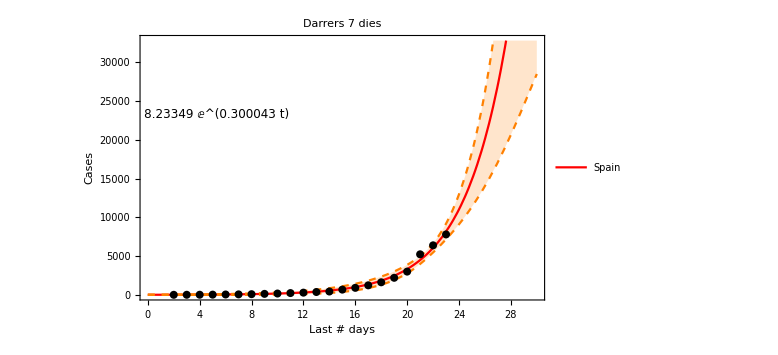

```mathematica
Plot[{fitspn,fitspi[[1]],fitspi[[2]]},{t,0,30},Epilog->{{Black,PointSize[0.01],Point[nw2sp]},{Text[Style[fitspn,Black,12],Scaled[{0.19,0.7}]]}},PlotStyle->{Directive[Red],Directive[Orange,Dashed],Directive[Orange,Dashed],Directive[Black,Dashed],Blue},Frame->True,FrameStyle->Directive[Black,Bold,16],FrameLabel->{"Last # days","Cases"},PlotLegends->Placed[{"Spain"},{0.15,0.8}],ImageSize->Large,Axes->False,Filling->{2->{3}},PlotLabel->"Darrers 7 dies"]
```

```mathematica
tabgr=Table[{i,(nw2sp[[i+1,2]]-nw2sp[[i,2]])/nw2sp[[i,2]]*1.},{i,21}]
```

{{1,1.},{2,0.75},{3,0.857143},{4,0.730769},{5,0.311111},{6,0.423729},{7,0.488095},{8,0.352},{9,0.349112},{10,0.236842},{11,0.294326},{12,0.178082},{13,0.567442},{14,0.341246},{15,0.357301},{16,0.320293},{17,0.358025},{18,0.363636},{19,0.744},{20,0.221521},{21,0.220466}}

```mathematica
med={{0,Median[tabgr[[All,2]]]},{30,Median[tabgr[[All,2]]]}}
```

{{0,0.357301},{30,0.357301}}

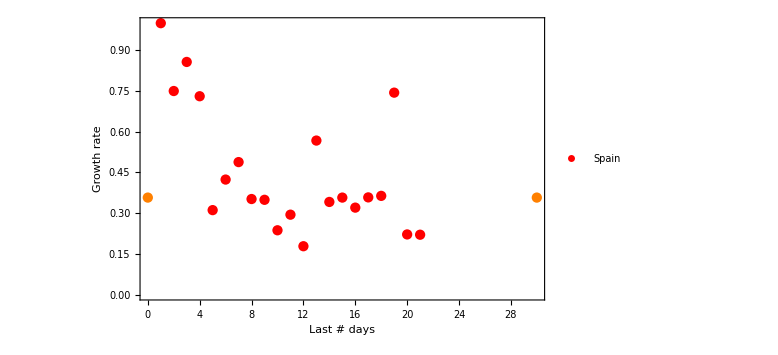

```mathematica
ListPlot[{tabgr,med},PlotStyle->{Directive[Red],{Join->True,Orange},Directive[Orange,Dashed],Directive[Black,Dashed],Blue},Frame->True,FrameStyle->Directive[Black,Bold,16],FrameLabel->{"Last # days","Growth rate"},PlotLegends->Placed[{"Spain"},{0.5,0.9}],ImageSize->Large,Axes->False]
```

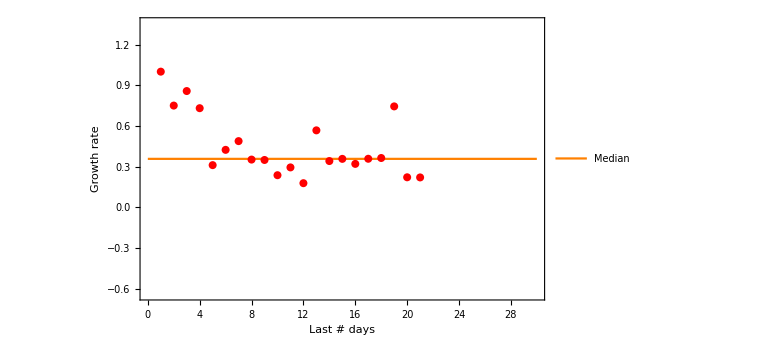

```mathematica
Plot[{0.3573008849557522},{t,0,30},PlotRange->All, Epilog->{{Red,PointSize[0.01],Point[tabgr]}},PlotStyle->{Directive[Orange]},Frame->True,FrameStyle->Directive[Black,Bold,16],FrameLabel->{"Last # days","Growth rate"},PlotLegends->Placed[{"Median"},{0.15,0.8}],ImageSize->Large,Axes->False]
```

```mathematica
nw2spd=nw2sp[[4;;-1]];
```

```mathematica
fitsp=NonlinearModelFit[nw2spd,b Exp[a t],{b,a},t]
```

FittedModel[7.55724 ⅇ^(0.303903 t)]

```mathematica
fitspn=Normal@fitsp
```

7.55724 ⅇ^(0.303903 t)

```mathematica
fitspi=fitsp["MeanPredictionBands",ConfidenceLevel->0.99]
```

{7.55724 ⅇ^(0.303903 t)-2.89823 √(ⅇ^(0.607806 t) (4.40862-0.402158 t+0.00922187 t^2)),7.55724 ⅇ^(0.303903 t)+2.89823 √(ⅇ^(0.607806 t) (4.40862-0.402158 t+0.00922187 t^2))}

```mathematica
datunc1=Flatten[fitspi[[1]]/.t->{nw2spd[[All,1]]}]
```

{13.0636,19.4182,28.6371,41.9523,61.109,88.574,127.827,183.768,263.282,376.022,535.493,760.526,1077.26,1521.66,2142.36,3002.,4169.54,5689.78,7595.12}

```mathematica
tabgr1=Table[{i,(datunc1[[i+1]]-datunc1[[i]])/datunc1[[i]]*1.},{i,Length@nw2spd-1}]
```

{{1,0.486432},{2,0.474756},{3,0.464965},{4,0.456631},{5,0.449443},{6,0.443168},{7,0.437629},{8,0.432683},{9,0.428211},{10,0.424101},{11,0.420236},{12,0.416464},{13,0.412531},{14,0.407909},{15,0.401259},{16,0.388919},{17,0.364608},{18,0.334869}}

```mathematica
datunc2=Flatten[fitspi[[2]]/.t->{nw2spd[[All,1]]}]
```

{56.0097,74.1856,98.2089,129.941,171.831,227.091,299.942,395.919,522.274,688.514,907.099,1194.38,1571.91,2068.33,2722.57,3590.65,4764.41,6416.94,8811.16}

```mathematica
tabgr2=Table[{i,(datunc2[[i+1]]-datunc2[[i]])/datunc2[[i]]*1.},{i,Length@nw2spd-1}]
```

{{1,0.324514},{2,0.323827},{3,0.323112},{4,0.32237},{5,0.321599},{6,0.320802},{7,0.319982},{8,0.319144},{9,0.318301},{10,0.317474},{11,0.316707},{12,0.316087},{13,0.315804},{14,0.316314},{15,0.318845},{16,0.326894},{17,0.346849},{18,0.373109}}

```mathematica
tabgr1i=Interpolation@tabgr1
```

InterpolatingFunction[…]

```mathematica
tabgr2i=Interpolation@tabgr2
```

InterpolatingFunction[…]

InterpolatingFunction::dmval: Input value {0.000429} lies outside the range of data in the interpolating function. Extrapolation will be used.

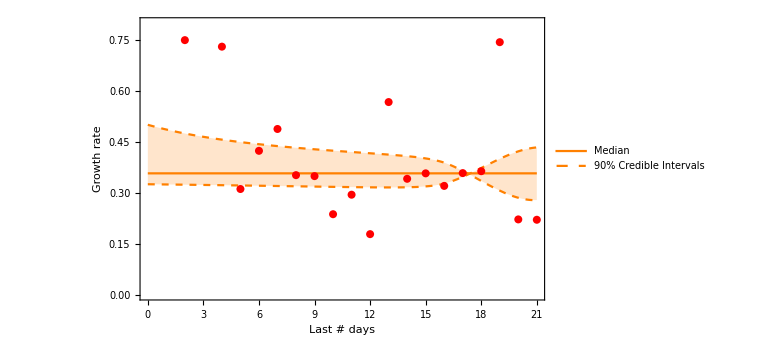

```mathematica
Plot[{0.3573008849557522,tabgr1i@t,tabgr2i@t},{t,0,21},PlotRange->{0,0.8}, Epilog->{{Red,PointSize[0.01],Point[tabgr]}},PlotStyle->{{Directive[Orange]},{Directive[Orange,Dashed]},{Directive[Orange,Dashed]}},Frame->True,FrameStyle->Directive[Black,Bold,16],FrameLabel->{"Last # days","Growth rate"},PlotLegends->Placed[{"Median","90% Credible Intervals"},{0.15,0.8}],ImageSize->Large,Axes->False,Filling->{2->{3}}]
```

## Chile

```mathematica
nws={{1,1},{2,3},{3,4},{5,5},{6,7},{7,10},{8,13},{9,17},{10,23},{11,34},{12,43},{13,61}};
```

```mathematica
nw2ch=nws/.{xx_,yy_}->{xx+7,yy}
```

{{8,1},{9,3},{10,4},{12,5},{13,7},{14,10},{15,13},{16,17},{17,23},{18,34},{19,43},{20,61}}

```mathematica
fitch=Normal@NonlinearModelFit[nw2ch,b Exp[a t],{b,a},t]
```

0.126583 ⅇ^(0.308379 t)

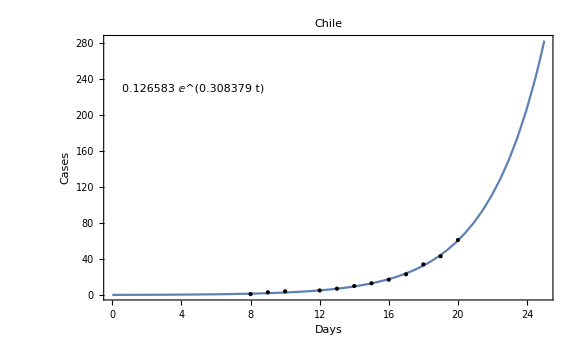

```mathematica
Plot[{fitch},{t,0,25},Epilog->{Point[nw2ch]},PlotRange->All,Frame->True,FrameStyle->Directive[Black,Bold,16],FrameLabel->{"Days","Cases"},PlotLegends->Placed[fitch,{0.2,0.8}],ImageSize->Large,PlotLabel->"Chile"]
```

## Italy

```mathematica
nwi={{3,12},{21,13},{79,14},{152,14},{229,25},{322,26},{471,27},{650,28},{888,29},{1128,30},{1694,31},{2036,32},{2502,33},{3089,34},{3858,35},{4636,36},{5883,37},{7275,38},{9712,39},{10149,40},{12462,41},{15113,42},{17660,43},{21150,44},{24747,45}};
```

```mathematica
nwi=Transpose[{Transpose[nwi][[2]],Transpose[nwi][[1]]}]
```

{{12,3},{13,21},{14,79},{14,152},{25,229},{26,322},{27,471},{28,650},{29,888},{30,1128},{31,1694},{32,2036},{33,2502},{34,3089},{35,3858},{36,4636},{37,5883},{38,7275},{39,9712},{40,10149},{41,12462},{42,15113},{43,17660},{44,21150},{45,24747}}

```mathematica
nw2i=nwi/.{xx_,yy_}->{xx-24,yy}
```

{{-12,3},{-11,21},{-10,79},{-10,152},{1,229},{2,322},{3,471},{4,650},{5,888},{6,1128},{7,1694},{8,2036},{9,2502},{10,3089},{11,3858},{12,4636},{13,5883},{14,7275},{15,9712},{16,10149},{17,12462},{18,15113},{19,17660},{20,21150},{21,24747}}

```mathematica
fitit=Normal@NonlinearModelFit[nw2i[[-21;;-1]],b Exp[a t],{a,b},t]
```

544.151 ⅇ^(0.182941 t)

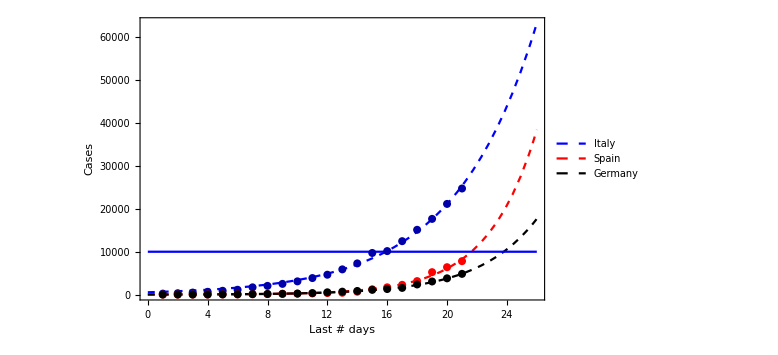

```mathematica
Plot[{fitit,fitspn,fitger,10^4},{t,0,26},Epilog->{{{Darker[Blue],PointSize[0.01],Point[nw2i/.{xx_,yy_}->{xx,yy}]}},{Red,PointSize[0.01],Point[nw2sp/.{xx_,yy_}->{xx,yy}]},{Black,PointSize[0.01],Point[nw2a/.{xx_,yy_}->{xx,yy}]}},PlotStyle->{Directive[Blue,Dashed],Directive[Red,Dashed],Directive[Black,Dashed],Blue},Frame->True,FrameStyle->Directive[Black,Bold,16],FrameLabel->{"Last # days","Cases"},PlotLegends->Placed[{"Italy","Spain","Germany"},{0.15,0.8}],ImageSize->Large,Axes->False,PlotRange->All]
```

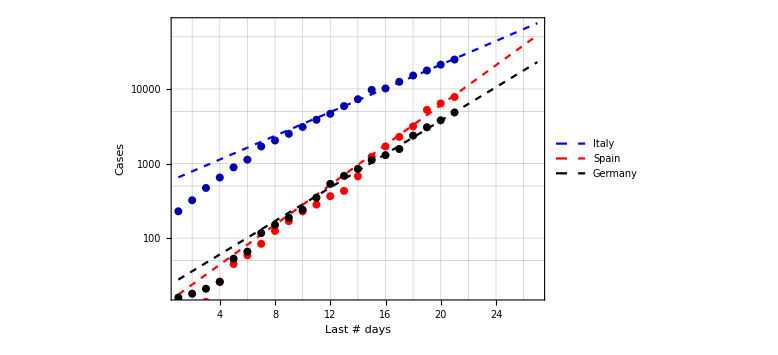

```mathematica
LogPlot[{fitit,fitspn,fitger},{t,1,27},Epilog->{{{Darker[Blue],PointSize[0.01],Point[nw2i/.{xx_,yy_}->{xx,Log@yy}]}},{Red,PointSize[0.01],Point[nw2sp/.{xx_,yy_}->{xx,Log@yy}]},{Black,PointSize[0.01],Point[nw2a/.{xx_,yy_}->{xx,Log@yy}]}},PlotStyle->{Directive[Blue,Dashed],Directive[Red,Dashed],Directive[Black,Dashed],Directive[Orange,Dashed],Directive[Darker[Red],Dashed],Blue},Frame->True,FrameStyle->Directive[Black,Bold,16],FrameLabel->{"Last # days","Cases"},PlotLegends->Placed[{"Italy","Spain","Germany"},{0.85,0.18}],ImageSize->Large,Axes->False,GridLines->All]
```

```mathematica
Length@nw2sp
```

21

```mathematica
Length@nw2a
```

21

```mathematica
tabesp=Table[{nw2sp[[i,1]],(nw2sp[[i+1,2]]-nw2sp[[i,2]])/nw2sp[[i,2]]*1.},{i,Length@nw2sp-1}]
```

{{1,1.},{2,0.75},{3,0.857143},{4,0.730769},{5,0.311111},{6,0.423729},{7,0.488095},{8,0.352},{9,0.349112},{10,0.236842},{11,0.294326},{12,0.178082},{13,0.567442},{14,0.826409},{15,0.376929},{16,0.343363},{17,0.381643},{18,0.663064},{19,0.221521},{20,0.220153}}

```mathematica
tabit=Table[{nw2i[[i,1]],(nw2i[[i+1,2]]-nw2i[[i,2]])/nw2i[[i,2]]*1.},{i,Length@nw2i-1}]
```

{{-11,6.},{-10,2.7619},{-9,0.924051},{-9,0.506579},{2,0.406114},{3,0.462733},{4,0.380042},{5,0.366154},{6,0.27027},{7,0.501773},{8,0.201889},{9,0.22888},{10,0.234612},{11,0.248948},{12,0.201659},{13,0.268982},{14,0.236614},{15,0.334983},{16,0.0449959},{17,0.227904},{18,0.212727},{19,0.16853},{20,0.197622},{21,0.170071}}

```mathematica
tabgr=Table[{nw2a[[i,1]],(nw2a[[i+1,2]]-nw2a[[i,2]])/nw2a[[i,2]]*1.},{i,Length@nw2a-1}]
```

{{1,0.125},{2,0.166667},{3,0.238095},{4,1.03846},{5,0.245283},{6,0.772727},{7,0.290598},{8,0.245033},{9,0.276596},{10,0.454167},{11,0.530086},{12,0.280899},{13,0.238304},{14,0.312869},{15,0.165468},{16,0.207562},{17,0.513738},{18,0.292528},{19,0.239386},{20,0.274835}}

```mathematica
medsp={{0,Median[tabesp[[All,2]]]},{500,Median[tabesp[[All,2]]]}}
```

{{0,0.379286},{500,0.379286}}

```mathematica
medit={{0,Median[tabit[[All,2]]]},{500,Median[tabit[[All,2]]]}}
```

{{0,0.258965},{500,0.258965}}

```mathematica
meda={{0,Median[tabgr[[All,2]]]},{500,Median[tabgr[[All,2]]]}}
```

{{0,0.275716},{500,0.275716}}

```mathematica
tabit[[-1,1]]-7
```

14

```mathematica
Median[tabit[[1;;-7,2]]]
```

0.350568

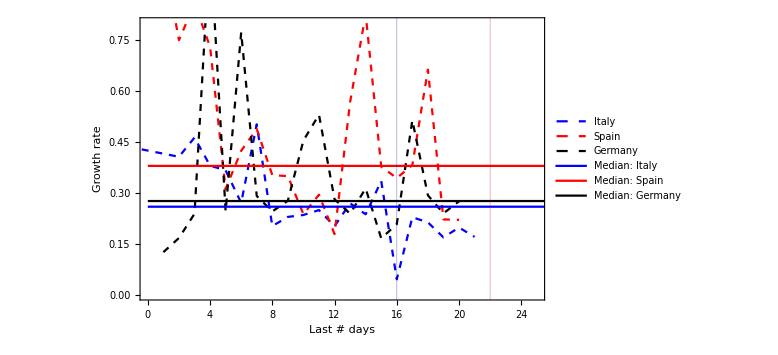

```mathematica
ListLinePlot[{tabit,tabesp,tabgr,medit,medsp,meda},Frame->True,FrameStyle->Directive[Black,Bold,16],FrameLabel->{"Last # days","Growth rate"},PlotStyle->{Directive[Blue,Dashed],Directive[Red,Dashed],Directive[Black,Dashed],Directive[Blue],Directive[Red],Directive[Black]},Frame->True,FrameStyle->Directive[Black,Bold,16],FrameLabel->{"Last # days","Cases"},PlotLegends->{"Italy","Spain","Germany","Median: Italy","Median: Spain","Median: Germany"},ImageSize->Large,Axes->False,PlotRange->{{0,25},{0,0.8}},GridLines->{{{16,Directive[Darker[Blue],Thick]},{22,Directive[Darker[Red],Thick]}}} ]
```

```mathematica
nw2inl=nw2i[[-21;;-7]];
fititnl=Normal@NonlinearModelFit[nw2inl,b Exp[a t],{a,b},t]
```

295.513 ⅇ^(0.231387 t)

```mathematica
tabitffitnl=Transpose[Flatten[Table[{t,fititnl},{t,{nw2sp[[All,1]]}}],1]][[All,2]];
```

```mathematica
tabeitNL=Table[{i,(tabitffitnl[[i+1]]-tabitffitnl[[i]])/tabitffitnl[[i]]*1.},{i,Length@tabitffitnl-1}]
```

{{1,0.260347},{2,0.260347},{3,0.260347},{4,0.260347},{5,0.260347},{6,0.260347},{7,0.260347},{8,0.260347},{9,0.260347},{10,0.260347},{11,0.260347},{12,0.260347},{13,0.260347},{14,0.260347},{15,0.260347},{16,0.260347},{17,0.260347},{18,0.260347},{19,0.260347},{20,0.260347}}

```mathematica
dates=Table[DatePlus[Today, n],{n,-23,0}];
```

```mathematica
dateplotit=Transpose[{dates,tabit[[All,2]]}];
dateplotitNL=Transpose[{dates[[5;;-1]],tabeitNL[[All,2]]}];
dateplotsp=Transpose[{dates[[5;;-1]],tabesp[[All,2]]}];
dateplotgr=Transpose[{dates[[5;;-1]],tabgr[[All,2]]}];
```

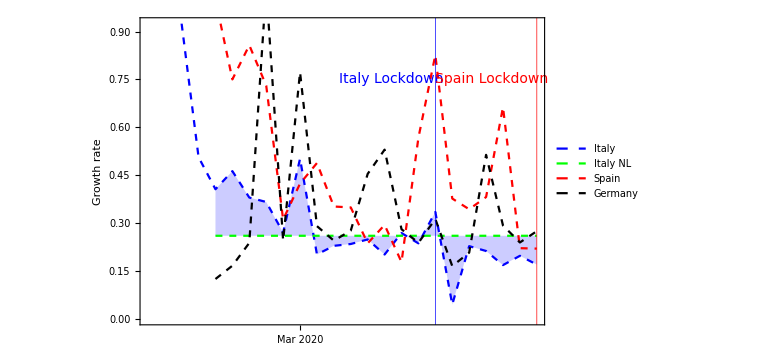

```mathematica
dp1=DateListPlot[{dateplotit,dateplotitNL,dateplotsp,dateplotgr},Frame->True,FrameStyle->Directive[Black,Bold,16],FrameLabel->{"","Growth rate"},PlotStyle->{Directive[Blue,Dashed],Directive[Green,Dashed],Directive[Red,Dashed],Directive[Black,Dashed],Directive[Blue],Directive[Red],Directive[Black]},ImageSize->Large,PlotLegends->{"Italy","Italy NL","Spain","Germany","Median"},ImageSize->Large,Axes->False,GridLines->{{{DateObject[List[2020,3,09],"Day","Gregorian",1.],Directive[Blue,Thick]},{DateObject[List[2020,3,15],"Day","Gregorian",1.],Directive[Red,Thick]}},None},GridLinesStyle->{{{Directive[Blue,Thick]},{Directive[Red,Thick]}},None},Epilog->{{Text[Style["Italy Lockdown",Blue,14],Scaled[{0.62,0.8}]]},Text[Style["Spain Lockdown",Red,14],Scaled[{0.87,0.8}]]},Filling->{1->{2}}]
```

```mathematica
Export["~/Desktop/GrowthRate.jpg",dp1]
```

~/Desktop/GrowthRate.jpg

```mathematica
npdays=Join[nw2sp[[All,1]],{22,23,24,25,26,27,28,29,30}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}

```mathematica
tabitffitnl=Transpose[Flatten[Table[{t,fititnl},{t,{npdays}}],1]][[All,2]];
tabitffit=Transpose[Flatten[Table[{t,fitit},{t,{Join[{-3,-2,-1,0},npdays]}}],1]][[All,2]];
tabitffsp=Transpose[Flatten[Table[{t,fitspn},{t,{npdays}}],1]][[All,2]];
tabitffgr=Transpose[Flatten[Table[{t,fitger},{t,{npdays}}],1]][[All,2]];
```

```mathematica
dates=Table[DatePlus[Today, n],{n,-24,9}];
```

```mathematica
dateplotitnl=Transpose[{dates[[5;;-1]],tabitffitnl}];
dateplotit=Transpose[{dates,tabitffit}];
dateplotsp=Transpose[{dates[[5;;-1]],tabitffsp}];
dateplotgr=Transpose[{dates[[5;;-1]],tabitffgr}];
```

```mathematica
Length@nw2i[[All,2]]
```

25

```mathematica
nw2i[[All,2]]
```

{3,21,79,152,229,322,471,650,888,1128,1694,2036,2502,3089,3858,4636,5883,7275,9712,10149,12462,15113,17660,21150,24747}

```mathematica
Length[dates[[1;;-10]]]
```

25

```mathematica
Length@nw2i[[All,2]]
```

25

```mathematica
dateplotitdnl=Transpose[{dates[[11;;-10]],nw2inl}];
dateplotitd=Transpose[{dates[[1;;-10]],nw2i[[All,2]]}];
dateplotspd=Transpose[{dates[[5;;-10]],nw2sp[[All,2]]}];
dateplotgrd=Transpose[{dates[[5;;-10]],nw2a[[All,2]]}];
```

```mathematica
fitit
fitspn
fitger
```

544.151 ⅇ^(0.182941 t)

12.9005 ⅇ^(0.307686 t)

21.4872 ⅇ^(0.258197 t)

```mathematica
dates
```

{Day: Fri 21 Feb 2020,Day: Sat 22 Feb 2020,Day: Sun 23 Feb 2020,Day: Mon 24 Feb 2020,Day: Tue 25 Feb 2020,Day: Wed 26 Feb 2020,Day: Thu 27 Feb 2020,Day: Fri 28 Feb 2020,Day: Sat 29 Feb 2020,Day: Sun 1 Mar 2020,Day: Mon 2 Mar 2020,Day: Tue 3 Mar 2020,Day: Wed 4 Mar 2020,Day: Thu 5 Mar 2020,Day: Fri 6 Mar 2020,Day: Sat 7 Mar 2020,Day: Sun 8 Mar 2020,Day: Mon 9 Mar 2020,Day: Tue 10 Mar 2020,Day: Wed 11 Mar 2020,Day: Thu 12 Mar 2020,Day: Fri 13 Mar 2020,Day: Sat 14 Mar 2020,Day: Sun 15 Mar 2020,Day: Mon 16 Mar 2020,Day: Tue 17 Mar 2020,Day: Wed 18 Mar 2020,Day: Thu 19 Mar 2020,Day: Fri 20 Mar 2020,Day: Sat 21 Mar 2020,Day: Sun 22 Mar 2020,Day: Mon 23 Mar 2020,Day: Tue 24 Mar 2020,Day: Wed 25 Mar 2020}

```mathematica
dp=DateListPlot[{dateplotit,dateplotitnl,dateplotsp,dateplotgr},Frame->True,FrameStyle->Directive[Black,Bold,16],FrameLabel->{"","Growth rate"},Epilog->{{{Darker[Blue],PointSize[0.01],Point[dateplotitd/.{xx_,yy_}->{xx,yy}]}},{Red,PointSize[0.01],Point[dateplotspd/.{xx_,yy_}->{xx,yy}]},{Black,PointSize[0.01],Point[dateplotgrd/.{xx_,yy_}->{xx,yy}]},{Text[Style["Italy Lockdown",Blue,14],Scaled[{0.62,0.8}]]},Text[Style["Spain Lockdown",Red,14],Scaled[{0.87,0.8}]]},PlotStyle->{Directive[Blue,Dashed],Directive[Green,Dashed],Directive[Red,Dashed],Directive[Black,Dashed],Directive[Blue],Directive[Red],Directive[Black]},ImageSize->Large,PlotLegends->Placed[{"Italy LD: Av. Growth=0.18","Italy NO LD: Av. Growth=0.23","Spain: Av. Growth=0.30","Germany: Av. Growth=0.25","Median: Italy=0.25","Median: Spain","Median: Germany"},{0.2,0.8}],ImageSize->Large,Axes->False,GridLines->{{{DateObject[List[2020,3,09],"Day","Gregorian",1.],Directive[Blue,Thick]},{DateObject[List[2020,3,15],"Day","Gregorian",1.],Directive[Red,Thick]}},None},GridLinesStyle->{{{Directive[Blue,Thick]},{Directive[Red,Thick]}},None},PlotRange->{{DateObject[List[2020,2,20],"Day","Gregorian",1.],DateObject[List[2020,3,25],"Day","Gregorian",1.]},{0,30000}}]
```

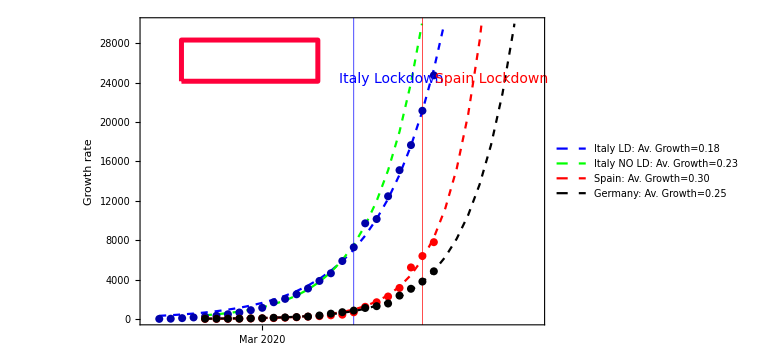

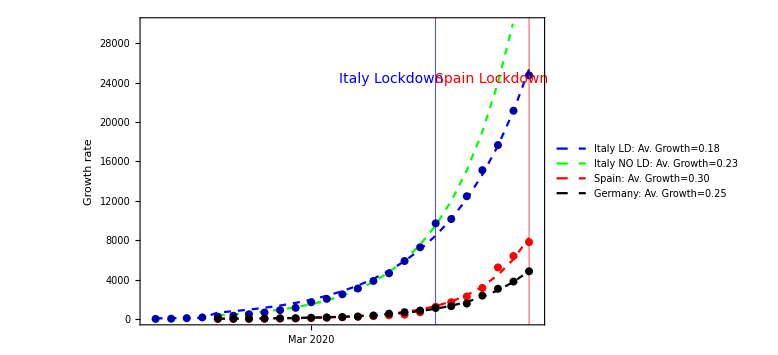

```mathematica
Export["~/Desktop/grate.jpg",-Graphics-]
```

~/Desktop/grate.jpg

```mathematica
DateListLogPlot[{dateplotit,dateplotsp,dateplotgr},Frame->True,FrameStyle->Directive[Black,Bold,16],FrameLabel->{"","Growth rate"},Epilog->{{{Darker[Blue],PointSize[0.01],Point[dateplotitd/.{xx_,yy_}->{xx,Log[yy]}]}},{Red,PointSize[0.01],Point[dateplotspd/.{xx_,yy_}->{xx,Log[yy]}]},{Black,PointSize[0.01],Point[dateplotgrd/.{xx_,yy_}->{xx,Log[yy]}]},{Text[Style["Italy Lockdown",Blue,14],Scaled[{0.62,0.8}]]},Text[Style["Spain Lockdown",Red,14],Scaled[{0.87,0.8}]]},PlotStyle->{Directive[Blue,Dashed],Directive[Red,Dashed],Directive[Black,Dashed],Directive[Blue],Directive[Red],Directive[Black]},ImageSize->Large,PlotLegends->Placed[{"Italy: Median=0.28","Spain: Median=0.35","Germany: Median=0.26","Median: Italy=0.25","Median: Spain","Median: Germany"},{0.2,0.8}],ImageSize->Large,Axes->False,GridLines->{{{DateObject[List[2020,3,09],"Day","Gregorian",1.],Directive[Blue,Thick]},{DateObject[List[2020,3,15],"Day","Gregorian",1.],Directive[Red,Thick]}},None},GridLinesStyle->{{{Directive[Blue,Thick]},{Directive[Red,Thick]}},None},PlotRange->{All,{0,30000}}]
```

-Graphics-

## UK prospects

```mathematica
(* We assume the same tendency as spain and a free propagation of the virus. UK has 60M inhabitants 60% of which could be infected at the end, that is, ~36M *)
```

```mathematica
DSolve[{n'[t]==0.3 n[t](1-n[t]/Nm)-0.99/15n[t],n[0]==1},n,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{n→Function[{t},(0.78 ⅇ^(0.234 t) Nm)/(1. ⅇ^(0.234 t)-0.78 (1.28205128205128-1. Nm)^1.)]}}

```mathematica
DSolve[nrec'[t]==C n[t],]
```

```mathematica
solmall=n/.NDSolve[{n'[t]==Chop[0.3 n[t](1-n[t]/10^7)-1/15 nrec[t]],nrec'[t]==1/15*99/100n[t],nrec[10]==1,n[0]==1},{n,nrec},{t,0,400}][[1]]
```

NDSolve::ndsz: At t == 97.014, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

```mathematica
solrec=nrec/.NDSolve[{n'[t]==Chop[0.3 n[t](1-n[t]/(10^7))-1/15 nrec[t]],nrec'[t]==1/15*99/100n[t],nrec[10]==1,n[0]==1},{n,nrec},{t,0,400}][[1]]
```

NDSolve::ndsz: At t == 97.014, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

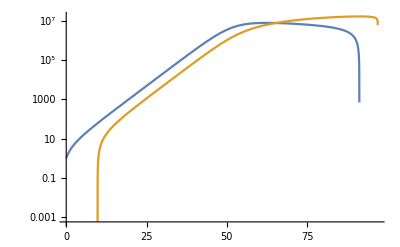

```mathematica
LogPlot[{solmall@t,solrec@t},{t,0,97}]
```

```mathematica
fun=0.4988888888888888 Nm-3.182054049600531*^-14 √Nm √(2.4580604479876906*^26 Nm-2.1946859422214396*^26 C[1]) Tanh[1/(√Nm)6.750155989723949*^-15 √(2.4580604479876906*^26 Nm-2.1946859422214396*^26 C[1]) (-1.4142135623730951 t-6.28524836104238*^14 Nm C[2])]/.Nm->10^6
```

498889.-3.18205×10^-11 √(2.45806×10^32-2.19469×10^26 C[1]) Tanh[6.75016×10^-18 √(2.45806×10^32-2.19469×10^26 C[1]) (-1.41421 t-6.28525×10^20 C[2])]

```mathematica
funt=fun/.C[1]->10^(6)/.C[2]->10^(-20)
```

498889.-163303. Tanh[0.0346418 (-6.28525-1.41421 t)]

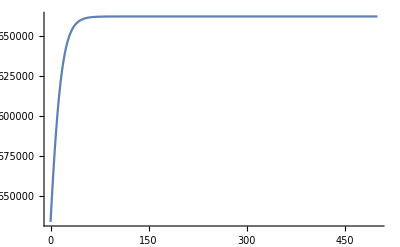

```mathematica
Plot[funt,{t,0,500},PlotRange->All]
```

```mathematica
fu1=fun/.t->0
```

498889.-3.18205×10^-11 √(2.45806×10^32-2.19469×10^26 C[1]) Tanh[6.75016×10^-18 √(2.45806×10^32-2.19469×10^26 C[1]) (0.-6.28525×10^20 C[2])]

```mathematica
fu2=Simplify[D[fun,t]]
```

3.03764×10^-28 (2.45806×10^32-2.19469×10^26 C[1]) Sech[9.54616×10^-18 √(2.45806×10^32-2.19469×10^26 C[1]) (1. t+4.44434×10^20 C[2])]^2

```mathematica
NSolve[{fu1==1,fu2==0.3},{C[1],C[2]}]
```

$Aborted

```mathematica
Chop[fun/.t->0]
```

498889.

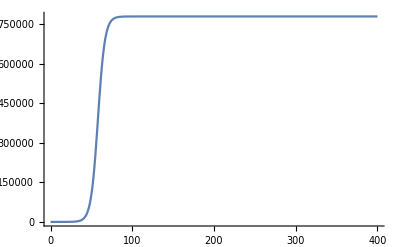

```mathematica
Plot[fun,{t,0,400},PlotRange->All]
```

```mathematica
Nm/(1+ ⅇ^(-A t)(Nm))
```

```mathematica
dn_dt =A n(1-n/nmax)- nreco/t
```

```mathematica
dnrec_dt=1/15 (0.99n)
```

```mathematica
DSolve[{n'[t]==0.3 n[t](1-n[t]/Nm)-1/15 nrec[t]n[t],nrec'[t]==1/15 (nrec[t]),nrec[0]==0,n[0]==1},{n,nrec},t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{}

```mathematica
nsp=7.223776944450219 ⅇ^(0.30126796572200387 (t));
```

```mathematica
nma=36 10^6;
nuk=nma/(nma(nsp^(-1))+1);
```

```mathematica
l1=.025;
l2=.001;
s=l1/2;
```

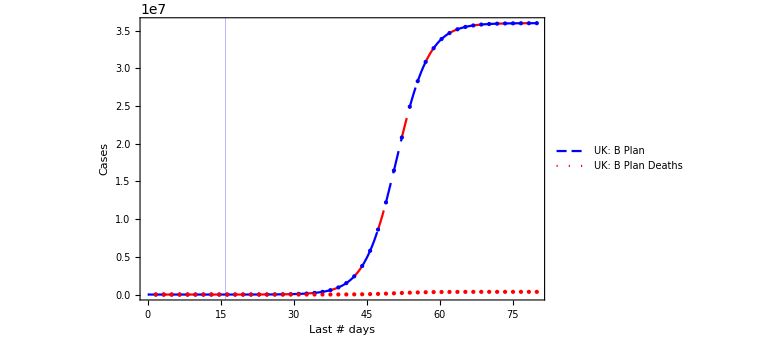

```mathematica
Plot[{nuk,nuk*0.01},{t,0,80},PlotStyle->{Directive[Blue,Dashing[{l1,s,l1,s,l1,s}]],Directive[Red,Dotted],Directive[Blue]},Mesh->Full,MeshFunctions->{#1&},MeshShading->{Red,Blue,Blue},Frame->True,FrameStyle->Directive[Black,Bold,16],GridLines->{{{16,Directive[Blue,Thick]}},None},FrameLabel->{"Last # days","Cases"},PlotLegends->Placed[{"UK: B Plan","UK: B Plan Deaths","UK: Today","Germany","Lower Saxony"},{0.45,0.8}],ImageSize->Large,Axes->False]
```

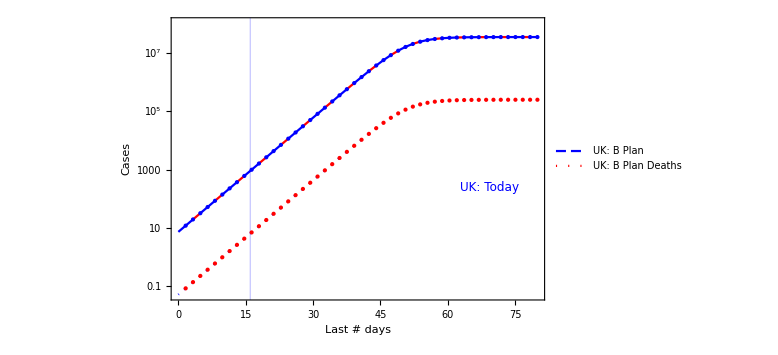

```mathematica
LogPlot[{nuk,nuk*0.007},{t,0,80},PlotRange->{{0,80},{0,3nma}},PlotStyle->{Directive[Blue,Dashing[{l1,s,l1,s,l1,s}]],Directive[Red,Dotted],Directive[Blue]},Mesh->Full,MeshFunctions->{#1&},MeshShading->{Red,Blue,Blue},Frame->True,FrameStyle->Directive[Black,Bold,16],GridLines->{{{16,Directive[Blue,Thick]}},None},FrameLabel->{"Last # days","Cases"},PlotLegends->Placed[{"UK: B Plan","UK: B Plan Deaths","UK: Today","Germany","Lower Saxony"},{0.85,0.5}],Epilog->{{Text[Style["UK: Today",Blue,12],Scaled[{0.852,0.4}]]}},ImageSize->Large,Axes->False,ImageSize->Large]
```